## Initialization

```mathematica
myPrint[msg_,rest_]:=Print[StringForm@@Flatten[{msg,rest}]];
g=9.81;
l=1;(*Pool length*)
h=0.3;(*Pool depth*)
tMax=2;
(*
True -> use number of intervals, compute the step;
False -> use the step size, compute number of intervals
*)
useNIntervals=False;
If[useNIntervals,(
xIntervals=250;
zIntervals=30;
),(*else*) (
stepTarget=0.01;
xIntervals=Ceiling[l/stepTarget];
zIntervals=Ceiling[h/stepTarget];
)]
n=xIntervals+1;
m=zIntervals+1;
numNodes=n*m;
Δx=N[l/xIntervals];
Δz=N[h/zIntervals];
τ=Min[Δx,Δz];
(*τ=0.01;*)
tIntervals=Ceiling[tMax/τ];
t=tIntervals+1;
τ=N[tMax/tIntervals];
xCoord=Table[Δx(i-1),{i,1,n}];
zCoord=Table[Δz(i-1),{i,1,m}];
tCoord=Table[τ(i-1),{i,1,t}];
index=Table[1+(i-1) +(j-1)n,{i,1,n},{j,1,m}];
myPrint["Number of points X,Z,T = (``, ``, ``)",{n,m,t}];
myPrint["Δx,Δz,τ = (``, ``, ``)",{Δx,Δz,τ}];

(*Surface variable*)
hInitial[x_]:=1/((0.2)2π)Exp[-0.5((x/l-0.3)/0.05)^2];
hVal=NIntegrate[hInitial[x],{x,0,l}]/l;
hNorm[x_]:=hInitial[x]-hVal;
(*Right boundary movement*)
rightSpeed=5;
rightDisplace[t_]:=-0.1Which[t*rightSpeed<1,3(t*rightSpeed)^2-2(t*rightSpeed)^3,t*rightSpeed<2,(t*rightSpeed-2)^2(2t*rightSpeed-1),True,0];
rightVelFunc=Simplify[D[rightDisplace[q],q]];
rightVel[t_]:=rightVelFunc/.{q->t};

(*Matrix helper*)
centerIdx=1;
leftIdx=2;
rightIdx=3;
bottomIdx=4;
topIdx=5;
```

Number of points X,Z,T = (51, 16, 101)

Δx,Δz,τ = (0.02, 0.02, 0.02)

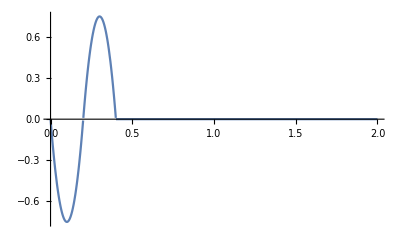

```mathematica
Plot[rightVel[x],{x,0,tMax}]
```

## Linear system of equations

```mathematica
buildMatrix[tIndex_Integer]:=Module[{i,j,result,center,left,right,bottom,top,mainIdx,tg},
(*Sparce matrix. We only need the center and 4 neighbors from each cell*)
result=Table[0.0,numNodes,numNodes];

(*Add contributions to nodes below the free surface*)
For[j=1,j≤m-1,j++,
For[i=1,i≤n,i++,
center=-2.0(Δx/Δz)-2.0(Δz/Δx);
left=right=Δz/Δx;
top=bottom=Δx/Δz;
If[i==1,
(*Left boundary*)
right+=left;
left=0;
];
If[i==n,
(*Right boundary*)
left+=right;
right=0;
];
If[j==1,
(*Bottom boundary*)
top+=bottom;
bottom=0;
];

mainIdx=index[[i,j]];
(*result[[mainIdx,centerIdx]]=center;
result[[mainIdx,leftIdx]]=left;
result[[mainIdx,rightIdx]]=right;
result[[mainIdx,bottomIdx]]=bottom;
result[[mainIdx,topIdx]]=top;*)
result[[mainIdx,mainIdx]]=center;
If[i>1,result[[mainIdx,index[[i-1,j]]]]=left;];
If[i<n,result[[mainIdx,index[[i+1,j]]]]=right;];
If[j>1,result[[mainIdx,index[[i,j-1]]]]=bottom;];
If[j<m,result[[mainIdx,index[[i,j+1]]]]=top;];
];
];

(*Add contributions to nodes on the free surface*)
tg=τ^2 g;
For[i=1,i≤n,i++,
center=-(4+tg/Δz+(tg Δz)/Δx^2);
left=right=(tg Δz)/(2 Δx^2);
bottom=tg/Δz;
top=0;
If[i==1,
(*Left boundary*)
right+=left;
left=0;
];
If[i==n,
(*Right boundary*)
left+=right;
right=0;
];

mainIdx=index[[i,m]];
(*result[[mainIdx,centerIdx]]=center;
result[[mainIdx,leftIdx]]=left;
result[[mainIdx,rightIdx]]=right;
result[[mainIdx,bottomIdx]]=bottom;
result[[mainIdx,topIdx]]=top;*)
result[[mainIdx,mainIdx]]=center;
If[i>1,result[[mainIdx,index[[i-1,j]]]]=left;];
If[i<n,result[[mainIdx,index[[i+1,j]]]]=right;];
If[j>1,result[[mainIdx,index[[i,j-1]]]]=bottom;];
If[j<m,result[[mainIdx,index[[i,j+1]]]]=top;];
];

Return[result];
];
buildRightSide[tIndex_Integer,ϕ_,hi_]:=Module[{result,i,tg,mainIdx},
result=Table[0.0,numNodes];
(*Contributions from nodes on the right boundary. Skip the free surface node*)
For[i=1,i<m,i++,
result[[index[[n,i]]]]=-2Δz rightVel[tCoord[[tIndex]]];
];

(*Contributions from nodes on the free surface*)
tg=τ g;
For[i=1,i≤n,i++,
mainIdx=index[[i,m]];
result[[mainIdx]]=-4ϕ[[mainIdx]]+τ(4 g hi[[i]]
+tg/Δz(ϕ[[mainIdx]]-ϕ[[index[[i,m-1]]]])
+(tg Δz)/Δx^2 ϕ[[mainIdx]]
-(tg Δz)/(2 Δx^2)(ϕ[[index[[If[i>1,i-1,i+1],m]]]]+ϕ[[index[[If[i<n,i+1,i-1],m]]]])
);
(*Right boundary contribution*)
If[i==n,result[[mainIdx]]+=(τ^2 g Δz)/Δx(rightVel[tCoord[[tIndex+1]]]+rightVel[tCoord[[tIndex]]])];
];
Return[result];
];
calcResudual[ϕ_,mat_,rhs_]:=Module[{resid,i,j,mainIdx},
resid=rhs;
For[i=1,i≤n,i++,
For[j=1,j≤m,j++,
mainIdx=index[[i,j]];
resid[[mainIdx]]-=mat[[mainIdx,centerIdx]]ϕ[[mainIdx]];
If[i>1,resid[[mainIdx]]-=mat[[mainIdx,leftIdx]]ϕ[[index[[i-1,j]]]]];
If[i<n,resid[[mainIdx]]-=mat[[mainIdx,rightIdx]]ϕ[[index[[i+1,j]]]]];
If[j>1,resid[[mainIdx]]-=mat[[mainIdx,bottomIdx]]ϕ[[index[[i,j-1]]]]];
If[j<m,resid[[mainIdx]]-=mat[[mainIdx,topIdx]]ϕ[[index[[i,j+1]]]]];
];
];
Return[resid];
];
buildInterpolation[hi_,xs_,ts_]:=Interpolation[Flatten[Table[{{xs[[i]],ts[[j]]},hi[[j,i]]},{j,1,t},{i,1,n}],1],InterpolationOrder->1];
```

## Solve system using Gauss-Seidel method

```mathematica
solutionH=None;
solutionF=Table[0,t];
Module[{tol,maxIterations,mat,rhs,i,j,k,ϕ,lastPhi,iter,toleranceMet,mainIdx,newValue,hi,kCurr,kPrev,resudual,elapseT,hRem,mRem,sRem,tTotal,tRem},Monitor[
hi=Table[0.0,{i,1,t},{j,1,n}];
(*For[i=1,i≤n,i++,hi[[1,i]]=hNorm[xCoord[[i]]]];*)
ϕ=Table[0.0,2,numNodes];
solutionF[[1]]=ϕ[[1]];

tol=N[10^-5];
maxIterations=500;
tTotal=0;
hRem=99;
mRem=99;
sRem=99;
For[k=2,k≤t,k++,
kCurr=1+Mod[k,2];
kPrev=1+Mod[k-1,2];
elapseT=AbsoluteTiming[
(*Note: mat is not actually a matrix. It only contains the non-zero elements from the real matrix*)
mat=buildMatrix[k-1];
rhs=buildRightSide[k-1,ϕ[[kPrev]],hi[[k-1]]];
(*ϕ[[kCurr]]=ϕ[[kPrev]];*)
iter=0;
toleranceMet=False;
lastPhi=0;
resudual={};

(*Solve for ϕ*)
(*myPrint["Solving for time index ``/`` (t=``/``) (``%)",{k,t,tCoord[[k]],tCoord[[t]],NumberForm[100.0(k-1)/t,{10,2}]}];*)
ϕ[[kCurr]]=LinearSolve[mat,rhs];
solutionF[[k]]=ϕ[[kCurr]];
(*While[iter<maxIterations,
lastPhi=ϕ[[kCurr]];
(*Update left to right*)
For[j=m,j≥1,j--,
For[i=1,i≤n,i++,
mainIdx=index[[i,j]];
newValue=rhs[[mainIdx]];
If[i>1,newValue-=mat[[mainIdx,leftIdx]]ϕ[[kCurr,index[[i-1,j]]]]];
If[i<n,newValue-=mat[[mainIdx,rightIdx]]ϕ[[kCurr,index[[i+1,j]]]]];
If[j>1,newValue-=mat[[mainIdx,bottomIdx]]ϕ[[kCurr,index[[i,j-1]]]]];
If[j<m,newValue-=mat[[mainIdx,topIdx]]ϕ[[kCurr,index[[i,j+1]]]]];
ϕ[[kCurr,mainIdx]]=newValue/mat[[mainIdx,centerIdx]];
];
];
(*Update right to left*)
For[j=m,j≥1,j--,
For[i=n,i≥1,i--,
mainIdx=index[[i,j]];
newValue=rhs[[mainIdx]];
If[i>1,newValue-=mat[[mainIdx,leftIdx]]ϕ[[kCurr,index[[i-1,j]]]]];
If[i<n,newValue-=mat[[mainIdx,rightIdx]]ϕ[[kCurr,index[[i+1,j]]]]];
If[j>1,newValue-=mat[[mainIdx,bottomIdx]]ϕ[[kCurr,index[[i,j-1]]]]];
If[j<m,newValue-=mat[[mainIdx,topIdx]]ϕ[[kCurr,index[[i,j+1]]]]];
ϕ[[kCurr,mainIdx]]=newValue/mat[[mainIdx,centerIdx]];
];
];
iter++;
(*resudual=calcResudual[ϕ[[kCurr]],mat,rhs];*)
If[Max[Abs[ϕ[[kCurr]]-lastPhi]]<tol,
toleranceMet=True;
Break[]];
]*);
(*Update the free surface height*)
For[i=1,i≤n,i++,
hi[[k,i]]=-(2/(τ g)(ϕ[[kCurr,index[[i,m]]]]-ϕ[[kPrev,index[[i,m]]]])+hi[[k-1,i]]);
];
][[1]];
tTotal+=elapseT;
tRem=tTotal(t-1)/(k-1)-tTotal;
hRem=Floor[tRem/3600];
mRem=Floor[Mod[tRem,3600]/60];
sRem=Floor[Mod[tRem,60]];
(*If[toleranceMet==False,
myPrint["Could not meet tolerance (``) for time index ``, Max residual was: ``",{tol,k,Max[Abs[ϕ[[kCurr]]-lastPhi]]}];
(*,myPrint["Tolerance met (``) for time index `` in `` iterations, Max error was: ``",{tol,k,iter,Max[Abs[ϕ[[kCurr]]-lastPhi]]}];*)
]*);
];
myPrint["Done!",{}];
solutionH=hi;

,Row[{ProgressIndicator[(k-1)/(t-1)],StringForm["``/``, Time remaining: ``h, ``m, ``s",(k-1),(t-1),hRem,mRem,sRem]}," "]];
];
ListPlot3D[solutionH,PlotRange->{-1,1},DataRange->{{0,l},{0,tMax}}]
```

Done!

-Graphics3D-

```mathematica
finiteSol=buildInterpolation[solutionH,xCoord,tCoord];
nF=20;(*Number of fourier coefficients*)
coeff=Table[2/l NIntegrate[hInitial[x]Cos[(i π)/l x],{x,0,l}],{i,1,nF}];
omega=Table[√((i π)/l g Tanh[(i π)/l h]),{i,1,nF}];
basis=Table[Cos[(i π)/l x]Cos[omega[[i]] time],{i,1,nF}];
Manipulate[
Show[
(*Plot[hNorm[x],{x,0,l},PlotRange->{-1,1},PlotStyle->Red],*)
Plot[finiteSol[x,t],{x,0,l},PlotRange->{-1,1},PlotStyle->Red]
(*,Plot[basis.coeff/.{time->t},{x,0,l},PlotRange->{-1,1}]*)
]
,{t,0,4π,AnimationRate->1/50,Appearance->"Open"}]
```